```mathematica
SquareWave[x]
```

```mathematica
f = SquareWave[x]
```

SquareWave[x]

0

```mathematica
D[SquareWave[x], x]
```

0

```mathematica
f = FourierSinSeries[SquareWave[x], x, 10, FourierParameters->{-Pi, Pi}]
```

(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π)

```mathematica
Simplify[(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π)]
```

(4 (15 Sin[2 π x]+5 Sin[6 π x]+3 Sin[10 π x]))/(15 π)

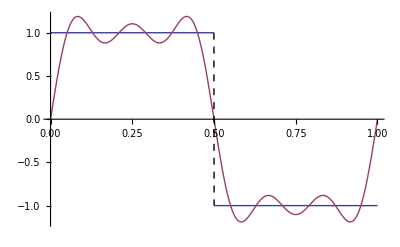

```mathematica
Plot[{SquareWave[x], f}, {x, 0, 1}, ExclusionsStyle->Dashed]
```

```mathematica
FourierSinSeries[SquareWave[x], x, 10, FourierParameters->{-Pi, Pi}]
```

(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π)

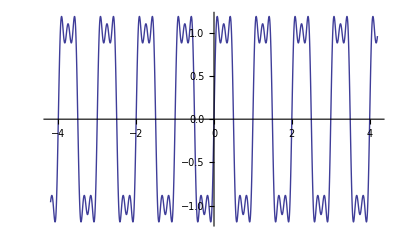

```mathematica
Plot[(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π),{x,-4.2,4.2}]
```

```mathematica
f = FourierSinSeries[SquareWave[x], x, 11, FourierParameters->{-Pi, Pi}]
```

(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π)

```mathematica
f2 = FourierSinSeries[SquareWave[x], x, 21, FourierParameters->{-Pi, Pi}]
```

(2^(3/2-π/2+(1+π)/2) Sin[2 π x])/π+(2^(3/2-π/2+(1+π)/2) Sin[6 π x])/(3 π)+(2^(3/2-π/2+(1+π)/2) Sin[10 π x])/(5 π)+(2^(3/2-π/2+(1+π)/2) Sin[14 π x])/(7 π)+(2^(3/2-π/2+(1+π)/2) Sin[18 π x])/(9 π)

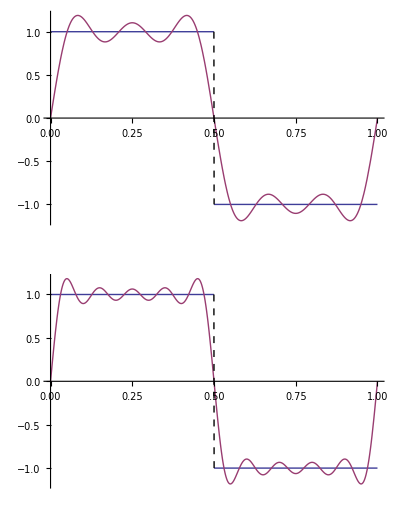

```mathematica
GraphicsColumn[{
Plot[{SquareWave[x], f}, {x, 0, 1}, ExclusionsStyle->Dashed],
Plot[{SquareWave[x], f2}, {x, 0, 1}, ExclusionsStyle->Dashed]
}]
```

```mathematica
Export["Dropbox/UNSW/honours-thesis/figures/fourier.pdf",%79,"PDF"]
```

Dropbox/UNSW/honours-thesis/figures/fourier.pdf

```mathematica
Sin[x]
```

Sin[x]

```mathematica
g = Normal[Series[Cos[x], {x, 0, 11}] ]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

```mathematica
g2 = Normal[ Series[Cos[x], {x, 0, 21}] ]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000+x^20/2432902008176640000

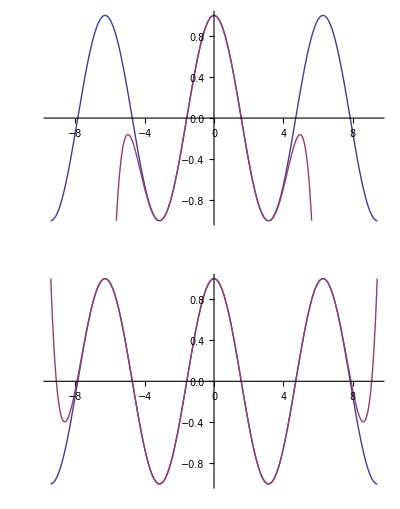

```mathematica
GraphicsColumn[{
Plot[{Cos[x], g}, {x, -3Pi, 3Pi},PlotRange->{-1, 1}, ExclusionsStyle->Dashed],
Plot[{Cos[x], g2}, {x, -3Pi, 3Pi},PlotRange->{-1, 1},  ExclusionsStyle->Dashed]
}]
```

```mathematica
Export["Dropbox/UNSW/honours-thesis/figures/taylor.pdf",%75,"PDF"]
```

Dropbox/UNSW/honours-thesis/figures/taylor.pdf

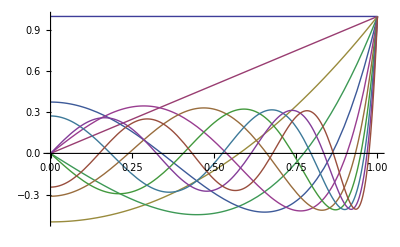

```mathematica
Plot[Evaluate @ Table[LegendreP[i,x], {i, 0, 10}],{x,0,1}]
```

```mathematica
Plot[Evaluate[Table[LegendreP[i,x],{i,0,10}]],{x,0,1},AbsoluteThickness[2.]]
```

Plot::nonopt: Options expected (instead of AbsoluteThickness[2.]) beyond position 3 in Plot[{1, x, 1/2\ (-1 + 3\ x^2), 1/2\ (-3\ x + 5\ x^3), 1/8\ (3 - 30\ x^2 + 35\ x^4), 1/8\ (15\ x - 70\ x^3 + 63\ x^5), 1/16\ (-5 + 105\ x^2 - 315\ x^4 + 231\ x^6), 1/16\ (-35\ x + 315\ x^3 - 693\ x^5 + 429\ x^7), 1/128\ (35 - 1260\ x^2 + 6930\ x^4 - 12012\ x^6 + 6435\ x^8), 1/128\ (315\ x - 4620\ x^3 + 18018\ x^5 - 25740\ x^7 + 12155\ x^9), 1/256\ (-63 + 3465\ x^2 - 30030\ x^4 + 90090\ x^6 - 109395\ x^8 + 46189\ x^10)}, {x, 0, 1}, AbsoluteThickness[2.]]. An option must be a rule or a list of rules.

Plot[{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5),1/16 (-5+105 x^2-315 x^4+231 x^6),1/16 (-35 x+315 x^3-693 x^5+429 x^7),1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8),1/128 (315 x-4620 x^3+18018 x^5-25740 x^7+12155 x^9),1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10)},{x,0,1},AbsoluteThickness[2.]]

```mathematica
Table[LegendreP[i,x], {i, 0, 10}]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5),1/16 (-5+105 x^2-315 x^4+231 x^6),1/16 (-35 x+315 x^3-693 x^5+429 x^7),1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8),1/128 (315 x-4620 x^3+18018 x^5-25740 x^7+12155 x^9),1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10)}

```mathematica
Export["Dropbox/UNSW/honours-thesis/figures/legendre.pdf",%89,"PDF"]
```

Dropbox/UNSW/honours-thesis/figures/legendre.pdf